```mathematica
calcBins[data_,start_,end_,binCount_]:=Block[{ret,idx},
ret=Table[0,{i,1,binCount}];
For[i=1,i<=Length[data],i++,
If[ data[[i]]>=start&&data[[i]]<end,
idx=Floor[((data[[i]]-start)binCount)/(end-start)]+1;
ret[[idx]]=ret[[idx]]+1;
];
];
Return[ret];
];
calcSS[data1_,data2_,data3_,cs1_,cs2_,cs3_,start_,binCount_]:=Block[{b1,b2,b3,minS,ret},
b1=Table[0,{i,1,binCount}];
b2=Table[0,{i,1,binCount}];
b3=Table[0,{i,1,binCount}];
ret=Table[0,{i,1,binCount}];
For[i=1,i<=binCount,i++,
minS=(1-start)/binCount*(i-1)+start;
b1[[i]]=Sum[If[data1[[j]]>=minS,1,0],{j,1,Length[data1]}];
b2[[i]]=Sum[If[data2[[j]]>=minS,1,0],{j,1,Length[data2]}];
b3[[i]]=Sum[If[data3[[j]]>=minS,1,0],{j,1,Length[data3]}];
];
For[i=1,i<=binCount,i++,
If[b3[[i]]>0,ret[[i]]=(b3[[i]]*cs3)/(√(b3[[i]]*cs3+b2[[i]]*cs2+b1[[i]]*cs1))]
];
Return[ret];
];
score[h_,n_]:=2^(-h/(2HarmonicNumber[n-1]-2(n-1)/n));
scorefast[h_,cn_]:=2^(-h/cn);
```

## V0 Results

## Fast Check

```mathematica
ToDipict=ToExpression[Import["F:\\PyworkingFolder\\CutExperiment\\Applications\\KMeans\\resultv0.csv","CSV"]];
```

```mathematica
listSM={};
listRR={};
listNP={};
Dynamic[prog]
ProgressIndicator[prog]
prog=0;
cn=N[2HarmonicNumber[Length[ToDipict]-1]-2(Length[ToDipict]-1)/Length[ToDipict]];
For[i=1,i<=Length[ToDipict],i++,
If[Round[ToDipict[[i,1]]]==0,AppendTo[listSM,scorefast[ToDipict[[i,2]],cn]]];
If[Round[ToDipict[[i,1]]]==1,AppendTo[listRR,scorefast[ToDipict[[i,2]],cn]]];
If[Round[ToDipict[[i,1]]]==2,AppendTo[listNP,scorefast[ToDipict[[i,2]],cn]]];
prog=prog+N[1/Length[ToDipict]];
]
```

## Results

```mathematica
HistoryData=ToExpression[Import["F:\\PyworkingFolder\\CutExperiment\\Applications\\KMeans\\historyv0.csv","CSV"]];
HistoryData2=ToExpression[Import["F:\\PyworkingFolder\\CutExperiment\\Applications\\KMeans\\historyv0-1.csv","CSV"]];
```

```mathematica
Length[HistoryData]
Length[HistoryData2]
```

40550

40550

```mathematica
listSM={};
listRR={};
listNP={};
maxl=1001;
ProgressIndicator[Dynamic[prog]]
prog=0;
cn=N[2HarmonicNumber[Length[HistoryData]-1]-2(Length[HistoryData]-1)/Length[HistoryData]];
For[i=1,i<=Length[HistoryData],i++,
If[Round[HistoryData[[i,1]]]==0,AppendTo[listSM,(scorefast[Mean[Take[HistoryData[[i]],{2,maxl}]],cn]+scorefast[Mean[Take[HistoryData2[[i]],{2,maxl}]],cn])/2]];
If[Round[HistoryData[[i,1]]]==1,AppendTo[listRR,(scorefast[Mean[Take[HistoryData[[i]],{2,maxl}]],cn]+scorefast[Mean[Take[HistoryData2[[i]],{2,maxl}]],cn])/2]];
If[Round[HistoryData[[i,1]]]==2,AppendTo[listNP,(scorefast[Mean[Take[HistoryData[[i]],{2,maxl}]],cn]+scorefast[Mean[Take[HistoryData2[[i]],{2,maxl}]],cn])/2]];
prog=prog+N[1/Length[HistoryData]];
]
```

```mathematica
listNP
```

{0.706472,0.766442,0.624931,0.633208,0.554933,0.609366,0.468538,0.565165,0.59818,0.703728,0.492399,0.573286,0.632545,0.455402,0.757976,0.688574,0.689379,0.663548,0.54934,0.752413,0.642734,0.517858,0.731328,0.662433,0.591055,0.61743,0.490081,0.825837,0.626304,0.384836,0.668047,0.683284,0.731511,0.618179,0.539154,0.574995,0.563943,0.60408,0.539741,0.486238,0.50895,0.698763,0.467995,0.667771,0.636892,0.630303,0.669817,0.562919,0.71179,0.68906}

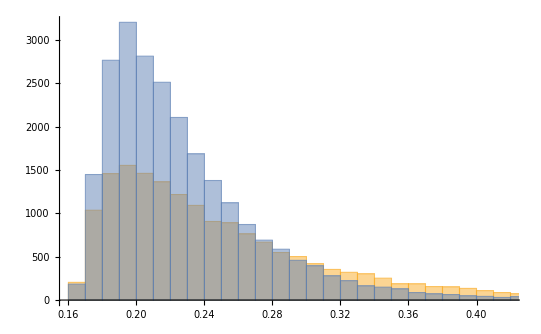

```mathematica
Histogram[{listSM,listRR},50]
```

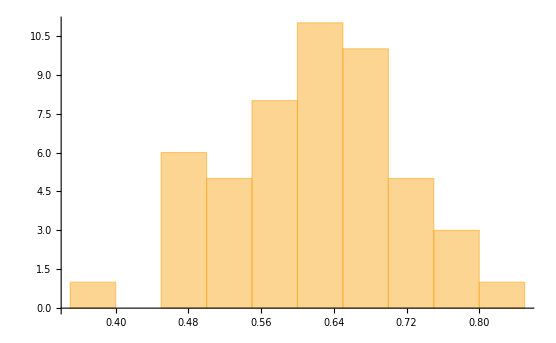

```mathematica
Histogram[{listNP},12]
```

```mathematica
calcBins[listNP,0.15,0.85,35]
calcBins[listSM,0.15,0.85,35]
calcBins[listRR,0.15,0.85,35]
```

{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,3,1,3,1,3,4,2,4,4,5,5,4,3,1,2,3,0,0,1,0}

{205,2497,3018,2582,2000,1655,1218,921,675,556,373,306,243,158,100,108,81,58,25,18,18,13,8,7,1,1,0,0,0,1,0,0,0,0,0}

{185,4218,6024,4623,3067,1994,1281,854,502,313,214,134,91,69,29,25,14,7,7,2,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Max[listSM]
```

0.745154

```mathematica
Sum[If[listNP[[n]]>Max[listSM],1,0],{n,1,50}]
```

4

```mathematica
calcSS[listSM,listRR,listNP,306.6/16846,430.5/23654,0.91/50,0.5,500]
```

{0.447557,0.451607,0.45437,0.45577,0.460049,0.464452,0.470523,0.472079,0.472079,0.468929,0.472175,0.472175,0.477171,0.478872,0.480592,0.48233,0.485864,0.489476,0.481428,0.483262,0.490813,0.492757,0.496715,0.49873,0.504926,0.509187,0.515786,0.518043,0.522648,0.522648,0.524997,0.527378,0.529792,0.532239,0.532239,0.53472,0.537236,0.539789,0.539789,0.547669,0.528788,0.528788,0.531479,0.536987,0.539806,0.542669,0.548536,0.551542,0.554598,0.557705,0.546483,0.546483,0.549615,0.552801,0.562703,0.554618,0.561595,0.561595,0.565183,0.572571,0.572571,0.572571,0.576376,0.572362,0.560368,0.564357,0.552191,0.556236,0.564601,0.564601,0.568928,0.568928,0.573355,0.573355,0.560891,0.552739,0.562029,0.571804,0.571804,0.571804,0.571804,0.571804,0.571804,0.576887,0.582108,0.582108,0.587473,0.598664,0.598664,0.604505,0.61052,0.61052,0.597446,0.597446,0.597446,0.610025,0.610025,0.610025,0.610025,0.603323,0.603323,0.617195,0.624499,0.624499,0.624499,0.611,0.61859,0.61859,0.61859,0.61859,0.612776,0.612776,0.612776,0.612776,0.621001,0.621001,0.629567,0.629567,0.615694,0.601546,0.610593,0.610593,0.610593,0.610593,0.610593,0.596211,0.596211,0.60124,0.611882,0.62311,0.62311,0.608522,0.608522,0.593592,0.578295,0.578295,0.578295,0.562602,0.562602,0.562602,0.562602,0.562602,0.575247,0.559345,0.559345,0.559345,0.559345,0.559345,0.559345,0.559345,0.559345,0.559345,0.559345,0.559345,0.559345,0.559345,0.559345,0.559345,0.559345,0.559345,0.559345,0.559345,0.559345,0.542991,0.526148,0.526148,0.526148,0.540565,0.523517,0.505903,0.487661,0.487661,0.487661,0.487661,0.487661,0.487661,0.487661,0.487661,0.487661,0.487661,0.487661,0.487661,0.487661,0.487661,0.468722,0.468722,0.468722,0.468722,0.468722,0.448999,0.406761,0.406761,0.406761,0.406761,0.406761,0.406761,0.406761,0.406761,0.406761,0.383953,0.383953,0.383953,0.383953,0.383953,0.359753,0.359753,0.359753,0.333879,0.333879,0.333879,0.333879,0.333879,0.305941,0.305941,0.305941,0.305941,0.305941,0.305941,0.305941,0.305941,0.305941,0.305941,0.305941,0.305941,0.305941,0.305941,0.305941,0.305941,0.305941,0.305941,0.305941,0.305941,0.241329,0.241329,0.241329,0.241329,0.241329,0.241329,0.241329,0.241329,0.241329,0.241329,0.241329,0.241329,0.241329,0.241329,0.269815,0.269815,0.269815,0.269815,0.269815,0.269815,0.269815,0.233666,0.233666,0.233666,0.233666,0.233666,0.190788,0.190788,0.190788,0.190788,0.190788,0.190788,0.190788,0.190788,0.190788,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
0.629
```

```mathematica
0.6257712082262211/(√(0.6257712082262211`+0.29+1.74*0.23*0.23))
```

0.738599

```mathematica
HistoryData[[1,1]]
HistoryData[[16847,1]]
HistoryData[[40501,1]]
```

0.

1.

2.

```mathematica
1/(√2000)StandardDeviation[Join[Take[HistoryData[[1]],{2,1001}],Take[HistoryData2[[1]],{2,1001}]]]/Mean[Join[Take[HistoryData[[1]],{2,1001}],Take[HistoryData2[[1]],{2,1001}]]]//N
1/(√2000)StandardDeviation[Join[Take[HistoryData[[16847]],{2,1001}],Take[HistoryData2[[16847]],{2,1001}]]]/Mean[Join[Take[HistoryData[[16847]],{2,1001}],Take[HistoryData2[[16847]],{2,1001}]]]//N
1/(√2000)StandardDeviation[Join[Take[HistoryData[[40501]],{2,1001}],Take[HistoryData2[[40501]],{2,1001}]]]/Mean[Join[Take[HistoryData[[40501]],{2,1001}],Take[HistoryData2[[40501]],{2,1001}]]]//N
```

0.00626643

0.00470869

0.00978686

```mathematica
pt1=Table[Mean[Take[HistoryData[[1]],{2,n}]],{n,2,1001}]//N
pt2=Table[Mean[Take[HistoryData[[16847]],{2,n}]],{n,2,1001}]//N
pt3=Table[Mean[Take[HistoryData[[40501]],{2,n}]],{n,2,1001}]//N
```

{27.,34.5,30.3333,31.5,31.,29.6667,28.4286,30.,30.6667,30.2,29.,29.8333,30.,29.9286,28.9333,29.25,29.1176,28.6667,28.5789,28.3,28.2857,29.1818,29.3478,30.,29.8,29.6538,30.0741,30.0357,30.2759,29.9,30.3548,30.0313,29.7879,29.6471,29.9429,29.8611,29.7568,29.3947,29.8462,29.725,30.0976,30.3333,30.2791,29.9318,29.9778,30.1522,29.9574,30.0208,30.3469,30.5,30.549,30.6923,30.6038,30.8519,30.8727,30.6964,30.5088,30.4483,30.3729,30.3,30.1639,30.2097,30.2222,30.0938,30.2,30.197,30.1642,30.1765,30.3478,30.3286,30.2113,30.1528,29.9726,29.9595,30.1467,30.0658,30.1948,30.2949,30.2658,30.45,30.4568,30.4634,30.4819,30.6667,30.5765,30.6163,30.5747,30.6477,30.6966,30.6444,30.6044,30.5761,30.5161,30.6277,30.7579,30.5833,30.6907,30.4694,30.5556,30.78,30.7723,30.6471,30.6311,30.625,30.619,30.6981,30.8411,30.8426,30.7248,30.7273,30.6937,30.7232,30.7611,30.8333,30.8609,30.819,30.8034,30.7373,30.7311,30.6417,30.6198,30.5082,30.4959,30.4839,30.472,30.5635,30.4882,30.5234,30.4729,30.5077,30.5496,30.5682,30.5564,30.5373,30.5778,30.5515,30.5328,30.529,30.5252,30.4786,30.5532,30.4507,30.4056,30.3958,30.4207,30.4315,30.3265,30.2838,30.2752,30.18,30.106,30.0855,30.1111,30.2208,30.1742,30.1346,30.1146,30.1076,30.0063,29.9938,30.0186,30.,29.9816,30.0427,30.0061,30.,29.976,29.9643,30.0178,30.0059,30.0643,30.0116,30.0231,30.069,30.0114,29.9489,29.9435,30.0562,29.9944,29.9944,30.0055,29.978,30.0273,30.0163,30.0162,30.0753,30.1283,30.0904,30.0265,30.0368,30.0157,29.9583,29.9585,29.9485,29.9487,29.9337,29.9645,29.9848,29.9698,29.99,30.0249,29.9851,30.0197,30.0833,30.1073,30.0825,30.0676,30.0385,29.9665,30.0381,30.0427,30.1462,30.1502,30.1636,30.1907,30.1852,30.212,30.1697,30.137,30.1591,30.1403,30.1441,30.1345,30.0759,30.1244,30.1283,30.1101,30.0658,30.0873,30.087,30.0736,30.0603,30.0472,30.0256,30.0255,29.9534,29.962,29.9832,29.9833,29.9917,30.,29.9959,29.9465,29.9836,29.9959,29.9472,29.9271,29.9718,30.,29.96,29.9004,29.9008,29.8814,29.9173,29.9412,29.957,29.93,29.9341,29.9305,29.8962,29.9272,29.9466,29.9696,29.947,29.9925,29.9624,29.985,29.9813,29.9591,29.9333,29.9668,29.9632,29.9414,29.8978,29.9018,29.9022,29.9278,29.9065,29.9319,29.9321,29.9039,29.8901,29.9435,29.9296,29.9649,29.8986,29.8676,29.9306,29.9827,29.9621,29.9794,29.9521,29.9386,29.9014,29.8983,29.9324,29.9125,29.906,29.9331,29.92,29.907,29.9371,29.9307,29.9507,29.9738,29.9902,29.9642,29.9286,29.9094,29.929,29.9357,29.9583,29.9553,29.949,29.9651,29.9399,29.9306,29.8962,29.8934,29.8813,29.8536,29.8634,29.8576,29.8426,29.8615,29.8865,29.896,29.8415,29.8024,29.8394,29.8489,29.8886,29.8979,29.8952,29.9045,29.8869,29.8487,29.8817,29.8938,29.8765,29.8387,29.7924,29.8309,29.8634,29.8493,29.8121,29.8069,29.7989,29.8309,29.8314,29.8177,29.8494,29.8385,29.8418,29.8254,29.7865,29.7927,29.8352,29.8273,29.8194,29.8532,29.8425,29.8292,29.7885,29.7836,29.7787,29.7575,29.7745,29.7561,29.7622,29.8005,29.7903,29.7962,29.7834,29.8,29.8644,29.8594,29.836,29.8443,29.8395,29.8451,29.8246,29.8146,29.8073,29.774,29.8057,29.814,29.7835,29.7686,29.7692,29.7801,29.7806,29.771,29.7817,29.7848,29.7879,29.7783,29.7563,29.7619,29.7825,29.7731,29.7687,29.7667,29.7896,29.758,29.7562,29.7371,29.7353,29.7531,29.722,29.7056,29.7087,29.6804,29.6763,29.6675,29.6659,29.6906,29.677,29.7088,29.6929,29.7007,29.6967,29.6903,29.6792,29.6753,29.6831,29.7026,29.6986,29.7016,29.7,29.6868,29.6898,29.7044,29.6912,29.7103,29.6789,29.659,29.653,29.656,29.6477,29.6712,29.69,29.6975,29.6757,29.6584,29.657,29.6376,29.6228,29.6169,29.6022,29.5765,29.5996,29.5872,29.5705,29.5934,29.5877,29.5536,29.5284,29.5185,29.513,29.5315,29.5152,29.5011,29.5086,29.5183,29.515,29.546,29.5705,29.6247,29.6064,29.5987,29.5763,29.5603,29.557,29.5874,29.5945,29.6101,29.5816,29.5595,29.5417,29.5489,29.556,29.5652,29.5785,29.5794,29.5926,29.6037,29.6004,29.6155,29.6061,29.6029,29.6016,29.5943,29.5951,29.5859,29.5706,29.5694,29.5643,29.5571,29.552,29.5449,29.5359,29.5388,29.5456,29.5386,29.5119,29.501,29.4961,29.499,29.4824,29.4736,29.4863,29.4834,29.5,29.5068,29.5233,29.5048,29.4961,29.499,29.5115,29.4971,29.4732,29.4761,29.4752,29.4571,29.4772,29.4516,29.4261,29.4423,29.4528,29.4539,29.453,29.4578,29.4569,29.4785,29.4776,29.4693,29.4461,29.4601,29.45,29.4566,29.4649,29.4604,29.4816,29.4899,29.478,29.479,29.4708,29.4463,29.4527,29.4392,29.4348,29.4322,29.4549,29.4559,29.446,29.4578,29.4695,29.4723,29.4696,29.492,29.5053,29.492,29.4823,29.4726,29.5265,29.5291,29.5352,29.536,29.5368,29.5534,29.5664,29.5567,29.5296,29.5287,29.533,29.5477,29.5329,29.5492,29.55,29.5422,29.5344,29.5163,29.5257,29.5333,29.5273,29.5315,29.5238,29.5348,29.5475,29.5482,29.5456,29.5464,29.532,29.5277,29.5369,29.5477,29.5184,29.5142,29.5117,29.5408,29.5598,29.5622,29.5662,29.5636,29.5594,29.5502,29.5609,29.5501,29.541,29.5434,29.5408,29.5791,29.5668,29.5854,29.5812,29.5608,29.5663,29.5428,29.5629,29.5684,29.5836,29.5827,29.5609,29.5728,29.5591,29.5662,29.5653,29.5517,29.5444,29.5578,29.5538,29.5577,29.5505,29.5449,29.5629,29.551,29.5439,29.529,29.4984,29.4852,29.4751,29.4728,29.4984,29.4822,29.4721,29.4822,29.466,29.473,29.4892,29.4869,29.4923,29.4747,29.4801,29.4595,29.4588,29.4353,29.421,29.4127,29.4455,29.466,29.4441,29.4389,29.4623,29.4526,29.4685,29.4588,29.4731,29.4918,29.4776,29.465,29.4732,29.4725,29.4718,29.4785,29.4808,29.4815,29.5015,29.5214,29.5265,29.5345,29.5132,29.5183,29.5,29.5387,29.5437,29.5284,29.5218,29.5196,29.5203,29.508,29.4971,29.4921,29.5086,29.505,29.4914,29.4892,29.5086,29.5021,29.4929,29.5036,29.5028,29.495,29.4773,29.4766,29.4618,29.4696,29.4845,29.4965,29.4972,29.4965,29.4888,29.5007,29.507,29.5189,29.5112,29.5258,29.5306,29.516,29.5236,29.5284,29.5263,29.5256,29.518,29.5048,29.5028,29.5048,29.5082,29.5213,29.5384,29.5171,29.5615,29.5525,29.5572,29.5429,29.5543,29.5658,29.5799,29.5683,29.5946,29.587,29.5849,29.5653,29.5618,29.5866,29.5724,29.5703,29.5816,29.5848,29.6027,29.5939,29.5824,29.5843,29.5729,29.5616,29.5582,29.5641,29.558,29.5534,29.55,29.5453,29.5367,29.5518,29.5759,29.5516,29.5535,29.5554,29.5638,29.5501,29.5403,29.5473,29.5518,29.5511,29.5388,29.5484,29.5451,29.5431,29.5566,29.5661,29.5564,29.5608,29.5639,29.5734,29.5638,29.5592,29.5369,29.5197,29.5178,29.5057,29.4899,29.4766,29.4659,29.4716,29.4622,29.4591,29.4611,29.4642,29.4599,29.4393,29.4525,29.4544,29.4526,29.4296,29.4229,29.4236,29.428,29.404,29.4072,29.4141,29.4099,29.4032,29.415,29.4305,29.4263,29.4294,29.4216,29.4259,29.4401,29.4249,29.4207,29.4202,29.41,29.4265,29.432,29.4412,29.4298,29.4305,29.4444,29.4391,29.4458,29.4597,29.4615,29.461,29.4628,29.4743,29.4737,29.4815,29.4797,29.4934,29.4893,29.4935,29.4846,29.4781,29.4739,29.4663,29.4704,29.4628,29.4729,29.4865,29.4847,29.4759,29.4812,29.4818,29.4918,29.4901,29.4813,29.4924,29.4942,29.4994,29.4977,29.4948,29.4954,29.4797,29.4641,29.4636,29.4503,29.4579,29.4447,29.4407,29.4264,29.4225,29.4186,29.4181,29.4222,29.4046,29.4041,29.4059,29.4146,29.4073,29.4,29.4064,29.4127,29.4213,29.4163,29.4215,29.4391,29.4329,29.4685,29.4499,29.4584,29.4444,29.4372,29.4412,29.4374,29.4335,29.442,29.4437,29.431,29.4294,29.4433,29.4517,29.4446,29.4585,29.4524,29.4519,29.4536,29.462,29.4824,29.4686,29.4626,29.4479,29.4287,29.4458,29.4245,29.4404,29.4454,29.4449,29.4553,29.4635,29.4696,29.4723,29.4631,29.4626,29.4481,29.4454,29.4406,29.4509,29.4644,29.4521,29.4462,29.4372,29.4421,29.4502,29.4411,29.4471,29.4444,29.4376,29.4254,29.4058,29.3957,29.3985,29.396,29.4125,29.4195,29.4138,29.4038,29.4013,29.3871,29.3836,29.3716,29.3733,29.3824,29.3725,29.3878,29.3885,29.4027,29.4065,29.4113,29.4108,29.4031,29.3985,29.4012,29.405,29.4004,29.3927,29.4172,29.4105,29.4081,29.4138,29.4144,29.4027,29.394,29.3895,29.4025,29.4,29.3934,29.3961,29.4039,29.3922,29.3867,29.3914,29.39,29.3917,29.3821,29.398,29.3884,29.3901,29.3947,29.3893,29.3808,29.3764,29.376,29.3948,29.3944,29.396,29.3865,29.3962,29.3858,29.3974,29.411}

{47.,52.5,54.6667,49.5,50.2,51.1667,52.8571,50.375,48.7778,48.2,47.2727,47.5833,47.3077,46.7143,45.3333,45.875,46.4706,46.4444,45.2105,45.35,45.2857,45.5909,45.7826,46.125,46.12,46.5,46.4074,46.1429,46.1379,46.7,46.8387,47.1563,47.2424,47.5882,47.3714,47.1111,47.,46.9737,47.1795,46.825,46.3902,46.0952,46.0465,46.2045,46.5556,46.7174,46.5957,46.4583,46.551,46.98,47.098,47.4808,47.6415,47.5,47.8182,47.7143,47.8421,47.5517,47.4915,47.4667,47.2787,47.4032,47.3333,47.3906,47.3846,47.3485,47.5373,47.3088,47.5072,47.6857,47.5634,47.7639,47.8904,47.9459,48.0133,48.1184,48.2078,48.2949,48.3797,48.225,48.2716,48.1951,48.1325,48.4762,48.4588,48.3605,48.5172,48.625,48.618,48.5,48.6044,48.7935,48.7957,49.,49.0105,48.7917,48.5876,48.6429,48.6566,48.85,48.901,48.8431,48.7184,48.6346,48.6381,48.5283,48.5888,48.5185,48.3028,48.3273,48.2252,48.1339,48.1416,48.2193,48.1739,48.25,48.3419,48.322,48.2689,48.2333,48.2562,48.1148,48.1301,48.121,48.112,48.0873,48.0866,48.1406,48.1938,48.1077,48.0687,48.0985,48.0075,48.0149,47.9481,48.0368,48.1022,48.087,48.0719,47.9071,47.9291,47.8732,47.8531,47.8681,47.8621,47.9178,47.8912,47.8243,47.8456,47.8533,47.8477,47.875,47.8039,47.6948,47.6258,47.5385,47.6561,47.6266,47.4969,47.4688,47.5714,47.5617,47.5767,47.5061,47.4545,47.4036,47.479,47.4881,47.3964,47.3647,47.3743,47.2791,47.2601,47.2701,47.2114,47.3466,47.3672,47.4326,47.4022,47.4278,47.4088,47.456,47.4426,47.3696,47.3459,47.3978,47.4652,47.5213,47.455,47.5105,47.5026,47.4688,47.5337,47.5619,47.5897,47.4847,47.5381,47.5455,47.4975,47.515,47.4279,47.3663,47.4138,47.3186,47.3415,47.3447,47.3768,47.3269,47.3541,47.3857,47.3318,47.4292,47.3944,47.4159,47.3767,47.3657,47.4055,47.4128,47.411,47.4227,47.4208,47.3919,47.3587,47.4063,47.4044,47.4469,47.4185,47.5,47.5546,47.5826,47.6061,47.6034,47.5966,47.594,47.5872,47.5763,47.6962,47.6807,47.6904,47.7042,47.6929,47.7355,47.6708,47.709,47.7551,47.8008,47.8462,47.871,47.8755,47.836,47.7291,47.7421,47.7747,47.8307,47.7922,47.8281,47.856,47.8101,47.8263,47.9115,47.9157,47.9695,47.943,47.9886,47.9509,47.9474,47.9888,47.9813,47.9851,48.0148,48.048,48.1103,48.0916,48.0876,48.0727,48.0725,48.0325,48.0504,48.1362,48.1286,48.0854,48.078,48.1767,48.1831,48.1825,48.1573,48.1115,48.0417,48.083,48.0655,48.0687,48.0548,48.0648,48.0884,48.0678,48.0811,48.1347,48.1107,48.1104,48.1233,48.0598,48.0728,48.0924,48.0362,47.9836,48.0163,47.9446,47.9708,47.9353,47.9677,47.9678,47.9487,47.9105,47.8822,47.8952,47.8797,47.8644,47.8302,47.7868,47.7719,47.7788,47.8106,47.8235,47.7623,47.7508,47.7761,47.8043,47.7835,47.7325,47.7091,47.7402,47.747,47.7447,47.7335,47.7552,47.7411,47.7804,47.7722,47.7906,47.8235,47.8592,47.8275,47.8688,47.875,47.942,47.9566,47.9712,47.9598,48.0201,48.0371,48.1254,48.125,48.1048,48.0847,48.0648,48.0646,48.0644,48.1034,48.078,48.1139,48.1247,48.1519,48.1543,48.0934,48.0767,48.0464,48.0381,48.0136,48.0081,48.027,48.0243,48.0296,47.9893,48.0134,48.0053,48.0106,48.0106,47.9974,48.,48.0132,47.9869,47.966,47.9556,47.9271,47.9065,47.9093,47.9406,47.933,47.9383,47.9231,47.9156,47.8903,47.9109,47.8528,47.8532,47.8813,47.8866,47.8693,47.8296,47.8325,47.8105,47.8308,47.8114,47.8416,47.8691,47.8448,47.8403,47.8799,47.8924,47.8976,47.8662,47.8568,47.8717,47.8382,47.8386,47.8149,47.8441,47.8445,47.8878,47.8976,47.905,47.9265,47.9078,47.9434,47.9529,47.9977,47.9836,48.,47.9557,48.007,47.9768,47.9398,47.9423,47.9747,47.9586,47.922,47.9405,47.9543,47.9613,47.9227,47.9524,47.9593,47.9323,47.9189,47.8944,47.9126,47.9329,47.9286,47.9577,47.9689,47.9401,47.927,47.9272,47.9229,47.9121,47.9101,47.9059,47.8777,47.8802,47.8978,47.8894,47.8636,47.933,47.9224,47.9204,47.9056,47.8972,47.9188,47.919,47.9191,47.9193,47.9258,47.8753,47.8713,47.9179,47.9055,47.8973,47.8808,47.8894,47.9375,47.9064,47.9585,47.9441,47.9587,47.9402,47.9239,47.9322,47.9242,47.9202,47.9429,47.9267,47.9228,47.9148,47.8806,47.8626,47.8528,47.8471,47.8193,47.8096,47.834,47.8044,47.7869,47.8052,47.7679,47.7941,47.8004,47.8185,47.8248,47.8035,47.7941,47.771,47.7813,47.7895,47.8016,47.8136,47.8333,47.8511,47.8958,47.921,47.8827,47.8733,47.887,47.9082,47.8874,47.901,47.9411,47.9431,47.9129,47.9168,47.9547,47.9736,47.9549,47.9568,47.9363,47.9103,47.9328,47.9106,47.881,47.8442,47.8278,47.8503,47.8413,47.814,47.8217,47.7927,47.7692,47.8026,47.7956,47.7905,47.7927,47.7985,47.788,47.7975,47.7852,47.8054,47.8399,47.8761,47.8781,47.8891,47.8964,47.8841,47.8843,47.8774,47.8794,47.8637,47.9258,47.9383,47.9225,47.9192,47.9211,47.9545,47.986,47.9599,47.9495,47.9409,47.9323,47.9307,47.9394,47.924,47.9534,47.9329,47.933,47.9348,47.9384,47.9419,47.9317,47.9693,47.9762,47.9474,47.9424,47.9662,47.9493,47.9747,47.968,47.9378,47.9715,47.9631,47.9498,47.9399,47.9217,47.9717,47.9767,47.9818,47.9719,47.9488,47.9208,47.944,47.9786,47.9409,47.9361,47.9362,47.9101,47.925,47.9218,47.9252,47.9302,47.9238,47.9434,47.9467,47.9355,47.9404,47.9405,47.9326,47.9167,47.9104,47.893,47.8979,47.9013,47.9253,47.9444,47.9556,47.9383,47.9415,47.9338,47.9402,47.9465,47.9199,47.9091,47.9077,47.8844,47.8565,47.8614,47.8663,47.8913,47.8589,47.8421,47.8161,47.8287,47.8382,47.8385,47.8218,47.8113,47.8086,47.8211,47.7985,47.8003,47.8356,47.8298,47.824,47.8621,47.8759,47.8565,47.8446,47.8464,47.8722,47.8544,47.8651,47.8578,47.9013,47.8851,47.8718,47.8676,47.8648,47.8472,47.8311,47.818,47.8168,47.8451,47.8483,47.8324,47.8488,47.8372,47.8331,47.8246,47.8482,47.8222,47.7933,47.7834,47.7881,47.7841,47.7742,47.7991,47.7763,47.7795,47.7727,47.7716,47.7762,47.7794,47.7539,47.75,47.7332,47.7208,47.6999,47.6989,47.6979,47.6813,47.669,47.685,47.708,47.7268,47.7243,47.7037,47.6999,47.6891,47.6811,47.6634,47.6987,47.7033,47.7065,47.7042,47.7115,47.6967,47.686,47.6547,47.6676,47.635,47.6369,47.6236,47.6379,47.6589,47.6635,47.6776,47.6767,47.6866,47.6871,47.6875,47.6811,47.6924,47.6874,47.673,47.6653,47.6833,47.6878,47.7003,47.7235,47.7319,47.7416,47.7553,47.7837,47.788,47.7883,47.8005,47.8021,47.7944,47.8026,47.7804,47.7609,47.7493,47.7734,47.7697,47.749,47.7625,47.7628,47.7696,47.766,47.7546,47.7549,47.7396,47.7373,47.726,47.7445,47.7565,47.7775,47.7661,47.7652,47.7693,47.7542,47.7725,47.7908,47.7923,47.7951,47.7992,47.8033,47.7883,47.7669,47.7379,47.7281,47.7348,47.7503,47.7696,47.7649,47.7614,47.7705,47.7695,47.7711,47.7751,47.7616,47.7794,47.7772,47.8,47.8152,47.818,47.8182,47.7886,47.8174,47.8189,47.8278,47.8119,47.8183,47.8185,47.7916,47.8103,47.813,47.8145,47.8233,47.8174,47.8384,47.8509,47.8437,47.8293,47.8234,47.8345,47.8226,47.8519,47.8545,47.8366,47.8343,47.837,47.8432,47.8446,47.8496,47.8594,47.8691,47.8777,47.8838,47.8804,47.8769,47.8926,47.8987,47.906,47.9049,47.9276,47.9371,47.9526,47.9562,47.9598,47.9469,47.9528,47.9647,47.9765,47.973,48.0023,48.0141,48.0059,48.0129,48.028,48.0327,48.0431,48.0384,48.0233,48.0186,48.0174,48.0336,48.0301,48.0324,48.0416,48.0358,48.0357,48.015,48.0138,48.0069,47.9989,47.9989,47.9954,47.9954,47.9783,47.9669,47.9692,47.9716,47.9523,47.958,47.9558,47.9411,47.9423,47.9469,47.9492,47.9459,47.9482,47.9381,47.9483,47.9484,47.954,47.9496,47.9553,47.9419,47.942,47.9242,47.9332,47.9266,47.9344,47.9334,47.9224,47.9402,47.9347,47.9381,47.9404,47.9361,47.935,47.9285,47.9473,47.9561,47.9638,47.9737,47.9694,47.9814,47.9934,48.0098,48.0054,48.0076,48.0109,47.9957,47.9859,47.9816,47.9643,47.9438,47.9341,47.932,47.9235,47.9311,47.914,47.9162,47.9185,47.9143,47.9058,47.9102,47.906,47.9007,47.9083,47.8903,47.8915,47.8831,47.8684,47.8727,47.8814,47.8698,47.8837,47.8817,47.8787,47.8788,47.8642,47.8623,47.8582,47.8562,47.8574,47.8503,47.8598,47.8683,47.8727,47.8613,47.8563,47.8543,47.8576,47.8494,47.86,47.8591,47.8561,47.849,47.8481,47.8566,47.8588,47.8363,47.8333,47.8284,47.8142,47.8174,47.832,47.8301,47.8333,47.8427,47.8327,47.8389,47.8299,47.8321,47.8293,47.8294,47.8327,47.8257,47.8279,47.8119,47.8212,47.8305,47.8558,47.856,47.8592,47.8663,47.8685,47.8706,47.8918,47.8889,47.897}

{10.,8.5,14.6667,13.25,11.,11.6667,12.,11.625,11.1111,10.9,10.7273,10.4167,9.92308,9.57143,9.33333,9.3125,9.52941,9.5,9.26316,9.5,9.57143,9.36364,9.43478,9.29167,9.36,9.38462,9.2963,9.21429,9.03448,9.06667,9.16129,9.03125,9.24242,9.20588,9.11429,9.16667,9.21622,9.13158,9.23077,9.325,9.43902,9.57143,9.60465,9.63636,9.62222,9.97826,9.95745,9.9375,10.0408,10.,9.94118,9.98077,10.0189,9.88889,9.83636,9.82143,9.92982,9.93103,9.94915,9.85,10.,9.98387,9.88889,9.95313,9.96923,10.,9.97015,10.0735,10.029,9.97143,9.90141,9.875,10.0274,9.90541,9.93333,9.86842,9.96104,10.0513,10.0886,10.025,9.97531,9.92683,9.87952,9.88095,9.88235,9.86047,9.83908,9.80682,9.82022,9.9,9.87912,9.86957,9.95699,10.,9.94737,9.86458,9.90722,9.97959,9.9697,9.97,9.94059,9.97059,10.0194,10.0096,9.95238,9.98113,9.99065,9.97222,9.99083,9.97273,9.95495,9.88393,9.83186,9.81579,9.78261,9.82759,9.82906,9.80508,9.78151,9.73333,9.80165,9.84426,9.91057,9.85484,9.872,9.89683,9.88976,9.875,9.89147,9.86154,9.84733,9.81061,9.82707,9.83582,9.82222,9.85294,9.91241,9.86232,9.8777,9.95,9.95745,9.97183,9.96503,9.97222,10.0069,9.96575,9.92517,9.89865,9.85906,9.82667,9.87417,9.84868,9.82353,9.84416,9.85806,9.82051,9.87261,9.8481,9.85535,9.84375,9.80124,9.7963,9.81595,9.82317,9.81212,9.80723,9.80838,9.78571,9.7574,9.77059,9.75439,9.72674,9.76301,9.74138,9.72571,9.70455,9.68927,9.66292,9.67039,9.67778,9.71823,9.68681,9.66667,9.66304,9.65946,9.64516,9.62032,9.70745,9.71958,9.74737,9.71728,9.72396,9.70984,9.72165,9.70256,9.68367,9.67513,9.64646,9.65327,9.665,9.65672,9.67327,9.66995,9.68627,9.70732,9.70874,9.7343,9.72596,9.73206,9.72381,9.72986,9.72642,9.70423,9.69626,9.70698,9.74074,9.73272,9.74771,9.71689,9.69545,9.70588,9.67117,9.67713,9.67411,9.69778,9.73009,9.72247,9.69737,9.68559,9.66957,9.67965,9.66379,9.65236,9.67949,9.6766,9.67797,9.68776,9.67647,9.68201,9.6875,9.70124,9.69008,9.68313,9.66393,9.64898,9.69106,9.68016,9.70565,9.68675,9.688,9.71315,9.72222,9.6996,9.70472,9.69412,9.69141,9.71984,9.74806,9.72973,9.74231,9.74713,9.74046,9.73764,9.72727,9.69811,9.69925,9.6779,9.66791,9.67658,9.6963,9.71956,9.72794,9.72894,9.72628,9.72,9.7029,9.72202,9.7554,9.75627,9.73571,9.74021,9.77305,9.78799,9.77465,9.77895,9.76923,9.79443,9.80208,9.80623,9.82759,9.82818,9.82534,9.83618,9.82993,9.86102,9.83446,9.83838,9.8557,9.85619,9.86667,9.87375,9.87086,9.88779,9.92105,9.94754,9.93464,9.93811,9.93831,9.94498,9.96129,9.99035,9.98397,9.97125,9.97771,9.99048,9.99367,9.99369,9.98742,9.97492,9.95938,9.97196,10.,9.98452,9.99383,9.99077,9.97853,10.0061,9.9939,10.0152,10.,10.0091,10.012,10.039,10.0509,10.0358,10.0387,10.0445,10.0325,10.0177,10.0147,10.0264,10.0205,10.0029,10.0116,10.0203,10.0029,10.0086,10.0057,9.98854,9.98,9.98006,9.96875,9.97734,9.98023,9.98873,9.98876,9.97759,10.,10.0084,10.0056,10.0139,9.99448,9.98072,9.97253,9.96164,9.96175,9.97275,9.97826,9.96748,9.97568,9.99461,9.98387,9.9866,9.99198,9.97867,9.98138,9.99735,10.0106,10.0158,10.0158,10.021,10.0262,10.0183,9.9974,10.,9.98964,9.97416,9.98454,9.97943,9.97179,9.95652,9.95663,9.95674,9.96447,9.96709,9.98737,9.99496,10.0075,9.99749,9.995,10.0125,10.0249,10.0397,10.0594,10.042,10.0296,10.0319,10.0196,10.022,10.039,10.0268,10.0413,10.0484,10.0435,10.041,10.0409,10.0288,10.0311,10.0167,10.031,10.0356,10.0332,10.0449,10.0519,10.08,10.0728,10.082,10.0794,10.0769,10.0837,10.0742,10.0694,10.0716,10.0829,10.108,10.1055,10.1098,10.1027,10.1071,10.1045,10.0998,10.086,10.0722,10.0631,10.0539,10.0448,10.0425,10.0603,10.0624,10.0756,10.082,10.0774,10.0684,10.0617,10.0549,10.0548,10.0547,10.0546,10.0392,10.05,10.0434,10.0346,10.0346,10.0345,10.0323,10.0408,10.0385,10.0449,10.0469,10.0638,10.0658,10.0657,10.0698,10.0738,10.0674,10.0651,10.0818,10.069,10.0647,10.0667,10.0603,10.0602,10.0476,10.0558,10.0701,10.0782,10.078,10.0943,10.09,10.0796,10.0774,10.0732,10.0629,10.0769,10.0747,10.0827,10.0845,10.0803,10.0721,10.082,10.0838,10.0896,10.0795,10.0714,10.0653,10.0692,10.0611,10.063,10.0629,10.0706,10.0665,10.0801,10.0643,10.0545,10.0447,10.0543,10.06,10.0695,10.0539,10.0577,10.0537,10.0479,10.0554,10.0573,10.0495,10.0646,10.0569,10.0492,10.0473,10.0642,10.081,10.0902,10.0844,10.0768,10.0598,10.0653,10.067,10.0688,10.0538,10.0574,10.0444,10.0517,10.0534,10.0441,10.0404,10.0403,10.0293,10.0255,10.0237,10.02,10.0181,10.029,10.0307,10.0199,10.0126,10.0234,10.0108,10.0072,10.0036,10.0375,10.0357,10.0427,10.0586,10.0514,10.0496,10.0495,10.0423,10.0493,10.0475,10.0491,10.0455,10.042,10.0593,10.0557,10.0643,10.0642,10.0763,10.0727,10.0725,10.0672,10.0723,10.0653,10.0583,10.0531,10.053,10.0512,10.0477,10.0459,10.0441,10.0305,10.022,10.027,10.027,10.0202,10.0235,10.0235,10.0352,10.0334,10.0367,10.0383,10.0333,10.0415,10.0398,10.048,10.0479,10.0413,10.0445,10.0576,10.0591,10.0492,10.0458,10.0458,10.0555,10.0537,10.0488,10.0649,10.0681,10.0696,10.0727,10.071,10.0789,10.0884,10.0867,10.0962,10.1072,10.1038,10.1037,10.1274,10.1383,10.1333,10.1252,10.1218,10.1248,10.1246,10.1244,10.1258,10.1162,10.1113,10.1064,10.1094,10.1139,10.109,10.1073,10.1087,10.1147,10.1269,10.1267,10.1204,10.1202,10.1169,10.1137,10.1212,10.1194,10.13,10.1252,10.1265,10.1172,10.1125,10.1138,10.1197,10.1271,10.1329,10.1403,10.1295,10.1263,10.1216,10.1214,10.1362,10.13,10.1284,10.1311,10.1369,10.1352,10.138,10.1304,10.1228,10.1211,10.1283,10.1414,10.1412,10.1424,10.1378,10.1376,10.1301,10.1241,10.1181,10.1179,10.1163,10.1161,10.1362,10.1317,10.1387,10.1457,10.147,10.1525,10.148,10.1607,10.1633,10.1559,10.1614,10.1598,10.1595,10.1579,10.1577,10.1617,10.1643,10.1627,10.1596,10.1509,10.1507,10.1477,10.1419,10.1417,10.1373,10.1469,10.1425,10.1506,10.1448,10.1419,10.1431,10.1387,10.1316,10.1286,10.1188,10.1131,10.1074,10.1073,10.1236,10.1262,10.1192,10.1135,10.1066,10.101,10.0954,10.0912,10.0856,10.0787,10.0854,10.0825,10.0865,10.0783,10.0863,10.0834,10.0847,10.0779,10.0791,10.0763,10.0842,10.0854,10.092,10.0945,10.0891,10.1062,10.1048,10.102,10.1111,10.107,10.1161,10.1107,10.1118,10.1091,10.1155,10.1114,10.1099,10.1176,10.124,10.1226,10.1159,10.117,10.1169,10.1141,10.1166,10.1242,10.1253,10.1239,10.116,10.1158,10.108,10.1091,10.1103,10.1152,10.1228,10.1315,10.1288,10.1261,10.1234,10.1207,10.1155,10.1128,10.1165,10.1113,10.1023,10.0958,10.0856,10.0818,10.0955,10.0954,10.0927,10.0864,10.0813,10.0774,10.0736,10.071,10.0659,10.077,10.0844,10.0867,10.0842,10.0853,10.0926,10.0937,10.0862,10.0812,10.0835,10.0859,10.0809,10.0808,10.0819,10.083,10.0805,10.0694,10.0754,10.0717,10.0704,10.0909,10.0993,10.1016,10.1171,10.1122,10.1084,10.1047,10.107,10.102,10.1007,10.1042,10.1065,10.1099,10.105,10.1144,10.1143,10.126,10.1306,10.134,10.1363,10.1349,10.1324,10.1417,10.138,10.1366,10.1353,10.134,10.1315,10.1348,10.1323,10.131,10.1285,10.1249,10.1235,10.1199,10.1256,10.1208,10.1183,10.1159,10.1285,10.1399,10.1386,10.143,10.1463,10.1438,10.154,10.1493,10.1571,10.1638,10.1625,10.1577,10.1655,10.1596,10.1583,10.1615,10.1557,10.151,10.1519,10.1427,10.1391,10.1458,10.1512,10.1454,10.1486,10.1519,10.164,10.1661,10.1771,10.1747,10.1723,10.1709,10.1641,10.1572,10.1526,10.1535,10.1533,10.1498,10.1452,10.1429,10.1438,10.1381,10.1302,10.1334,10.1311,10.1276,10.1242,10.124,10.1272,10.1205,10.1182,10.1235,10.1212,10.121,10.1253,10.1251,10.125,10.1216,10.1226,10.1224,10.1234,10.1265,10.121,10.1273,10.1272,10.1249,10.1237,10.1246,10.1245,10.1297,10.1338,10.1294,10.1282,10.1281,10.1322,10.131,10.1309,10.1243,10.1221,10.122,10.1314,10.128,10.1258,10.1183,10.1245,10.1328,10.1326,10.1377,10.1292,10.1312,10.1352,10.1382,10.1412,10.1379,10.1347,10.1366,10.1365,10.1322,10.1258,10.1256,10.1349,10.1306,10.1304,10.1231,10.1167,10.1197,10.1216,10.1256,10.1327,10.1398,10.1355,10.1405,10.1414,10.1392,10.1431,10.145,10.1418,10.1376,10.1344,10.1312,10.1301,10.1269,10.1268,10.1266,10.1215,10.1294,10.1313,10.1322,10.1341,10.139,10.1338,10.1337,10.1325,10.1314,10.1323,10.1401,10.142}

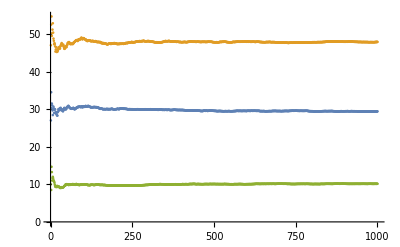

```mathematica
ListPlot[{pt1,pt2,pt3}]
```

```mathematica
(41/50*0.91)/(√(41/50*0.91+17/16846*0.91+6/23654*0.91))//N
```

0.863164

## V3 Results

```mathematica
ToDipict=ToExpression[Import["F:\\PyworkingFolder\\CutExperiment\\Applications\\KMeans\\resultv3.csv","CSV"]];
```

```mathematica
listSM={};
listRR={};
listNP={};
ProgressIndicator[Dynamic[prog]]
prog=0;
cn=N[2HarmonicNumber[Length[ToDipict]-1]-2(Length[ToDipict]-1)/Length[ToDipict]];
For[i=1,i<=Length[ToDipict],i++,
If[Round[ToDipict[[i,1]]]==0,AppendTo[listSM,2^((-ToDipict[[i,2]])/cn)]];
If[Round[ToDipict[[i,1]]]==1,AppendTo[listRR,2^((-ToDipict[[i,2]])/cn)]];
If[Round[ToDipict[[i,1]]]==2,AppendTo[listNP,2^((-ToDipict[[i,2]])/cn)]];
prog=prog+N[1/Length[ToDipict]];
]
```

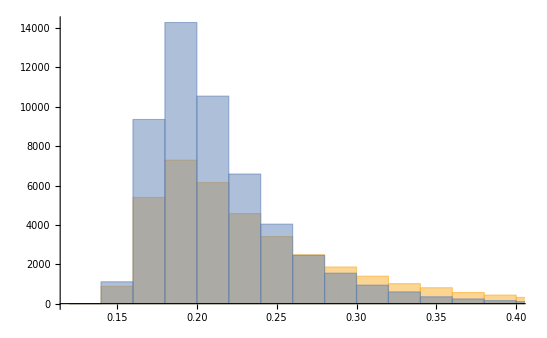

```mathematica
Histogram[{listSM,listRR},25]
```

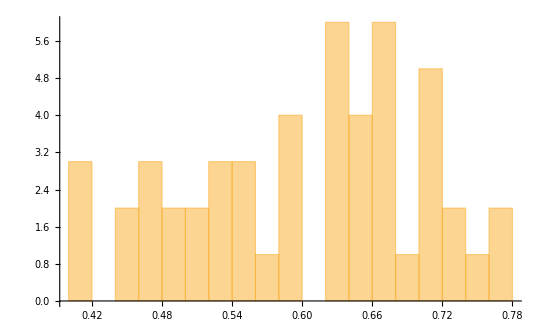

```mathematica
Histogram[{listNP},12]
```

```mathematica
calcBins[listNP,0.2,0.9,35]
calcBins[listSM,0.2,0.9,35]
calcBins[listRR,0.2,0.9,35]
```

```mathematica
calcSS[listSM,listRR,listNP,0.414/50,0.414/50,0.414/50,0.5,200]
```

{0.224866,0.230662,0.234947,0.24105,0.242025,0.245475,0.249692,0.246985,0.252185,0.257729,0.265984,0.267848,0.269559,0.273986,0.271107,0.268209,0.273095,0.275125,0.271345,0.26255,0.271529,0.281497,0.285528,0.289737,0.295651,0.301942,0.306933,0.31399,0.325552,0.329699,0.325721,0.332438,0.339588,0.322386,0.327308,0.329855,0.337869,0.331701,0.33747,0.328311,0.334335,0.337475,0.350979,0.350979,0.358369,0.370384,0.370384,0.374666,0.388462,0.393411,0.383793,0.388945,0.37453,0.37453,0.37453,0.353886,0.343205,0.354842,0.343927,0.32758,0.32758,0.32758,0.329802,0.329802,0.337563,0.313134,0.313134,0.308972,0.308972,0.318481,0.305431,0.291832,0.277611,0.277611,0.262679,0.262679,0.262679,0.262679,0.262679,0.262679,0.262679,0.242652,0.206356,0.206356,0.206356,0.206356,0.185742,0.185742,0.185742,0.185742,0.185742,0.185742,0.185742,0.20347,0.181989,0.157607,0.157607,0.157607,0.157607,0.157607,0.128686,0.128686,0.128686,0.128686,0.128686,0.0909945,0.0909945,0.0909945,0.0909945,0.0909945,0.0909945,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
0.297/(√(0.297`+0.29+1.74*0.23*0.23))
```

0.476163

```mathematica
(35/50*0.41)/(√(35/50*0.41+40/37390*0.41+13/52500*0.41))//N
```